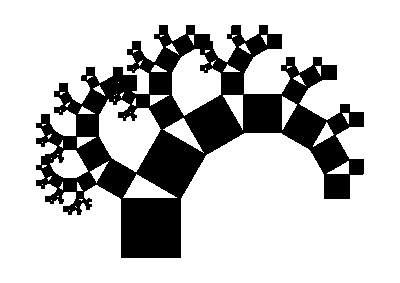

```mathematica
θ=60°;
depth=6;
Graphics[Polygon/@Partition[Join@@NestList[(TranslationTransform[{0,1}].ScalingTransform[{Cos[θ],Cos[θ]}].RotationTransform[θ])@#~Join~(TranslationTransform[{0,1}].ScalingTransform[{Sin[θ],Sin[θ]},{1,0}].RotationTransform[θ-90°,{1,0}])@#&,AnglePath[{0,1,1}Pi/2],depth],4]]
```